```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
```

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]];
rhovalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]];
Mass = 10^2;
threshold =(N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality})*0.1/.M->Mass
ExtinctionSigma = ParallelTable[
Reps = 1000;
ProportionExtinct=With[{
α=Resourcegrowth,λ=Growth,σ=sigma,ρ=rho,β=Maintenance,μ=Mortality,T=100000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0= (μ (-λ+σ))/(λ ρ+μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[5;;1001,1]];
Htraj = Flatten[Traj,1][[5;;1001,2]];
Rtraj = Flatten[Traj,1][[5;1001,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
```

1.63832

NDSolve::ndsz: At t == 17096.7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 154113., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 173402., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 6281.96, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 5186.21, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5348.75, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 4309.57, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 4833.49, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 8730.47, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 10298.5, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 7652.8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7078.49, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.55053×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 5.89328×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 5.84936×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.1449×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 5.86583×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 4.88072×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.34843×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 5.17104×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 5.69295×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 42812.5, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 35729.5, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 40243.7, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 138659., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 140763., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 148490., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 91345.9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 96197.3, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 68602.9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 95917.9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 79515.4, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 92170.9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 134175., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 99041.4, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 62537.3, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 95993.3, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 11180.6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 17224.8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.14538×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 7.09565×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 8.70514×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 8.17508×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 7.94253×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 7.43884×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 7.89545×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.94464×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.34197×10^7; unable to continue.

NDSolve::ndsz: At t == 66649.9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 9226.96, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 91373.8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 252.581, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 182.662, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 203.508, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.23904×10^7; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 1.00319×10^7; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 7.88546×10^7; unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 1.3582×10^6. Unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 5.62387×10^7; unable to continue.

General::stop: Further output of NDSolve :: ndcf will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 1.40818×10^6. Unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 1.81115×10^6. Unable to continue.

General::stop: Further output of NDSolve :: singls will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.54838×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 8.79902×10^7. Unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 6.42477×10^6; unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 4.82171×10^6. Unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 6.16109×10^7; unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 1.01182×10^7. Unable to continue.

General::stop: Further output of NDSolve :: singls will be suppressed during this calculation.

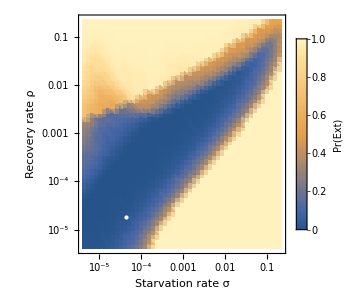

```mathematica
ExtPlot=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(4*10^-6),Log@0.224},{Log@(4*10^-6),Log@(0.224)}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}
```

{Log[-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])],Log[-(1.67857×10^-6)/(M^(1/4) Log[0.292893/(1-0.707107 (1-0.0202 M^0.19)^(1/4))])]}

```mathematica
Starvation
```

0.

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf",ExtPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf

```mathematica
threshold =(N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality})*0.2/.M->Mass
```

16.6738

```mathematica
Mass
```

10

```mathematica
ts=Table[t,{t,0,100000000,100000}];
```

```mathematica
ts[[5]]
```

400000

```mathematica
ts[[1001]]
```

100000000

```mathematica
4*10^5
```

400000

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]]
```

{4.×10^-6,5.×10^-6,6.25×10^-6,7.8125×10^-6,9.76563×10^-6,0.000012207,0.0000152588,0.0000190735,0.0000238419,0.0000298023,0.0000372529,0.0000465661,0.0000582077,0.0000727596,0.0000909495,0.000113687,0.000142109,0.000177636,0.000222045,0.000277556,0.000346945,0.000433681,0.000542101,0.000677626,0.000847033,0.00105879,0.00132349,0.00165436,0.00206795,0.00258494,0.00323117,0.00403897,0.00504871,0.00631089,0.00788861,0.00986076,0.012326,0.0154074,0.0192593,0.0240741,0.0300927,0.0376158,0.0470198,0.0587747,0.0734684,0.0918355,0.114794,0.143493,0.179366,0.224208}